```mathematica
regFuYear[x_]:= Piecewise[{{-x+5, x<1},{(x-2)^2+3, 1<=x<4},{x+3, x>=4}}]
```

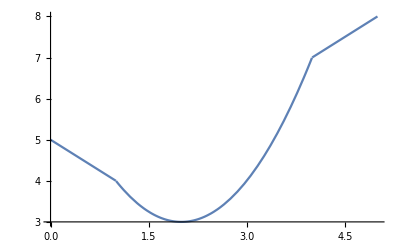

```mathematica
Plot[regFuYear[x], {x,0,5}]
```

```mathematica
timeLiYear=Table[(regFuYear[i]+RandomReal[{-.2,.2}]), {i,0,5,.1}]
```

{4.91852,4.94325,4.7313,4.73633,4.57175,4.65816,4.57567,4.15906,4.13428,4.29708,3.93472,3.70914,3.73814,3.29328,3.44474,3.29367,2.99506,3.03376,3.07837,2.96324,2.8349,3.16269,2.84384,3.1826,3.07749,3.29321,3.26905,3.30841,3.47191,3.71001,3.88563,4.30632,4.46006,4.56586,4.94533,5.15267,5.41499,5.71449,6.18349,6.5599,7.07271,7.20189,7.15089,7.35118,7.40033,7.54714,7.68809,7.62047,7.93219,8.04706,8.19845}

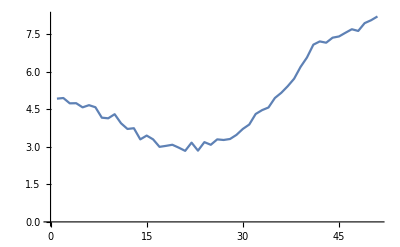

```mathematica
ListLinePlot[timeLiYear]
```

```mathematica
addYear=regFuYear[5]-regFuYear[0]
```

3